```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cd=ColorData[97,"ColorList"];
```

## Part 3 : Sampling

```mathematica
p1 = Import["outCTRNN.dat"];
p2A = Import["outCC.dat"];
p2B = Import["outCCO.dat"];
p3 = Import["outHP.dat"];
```

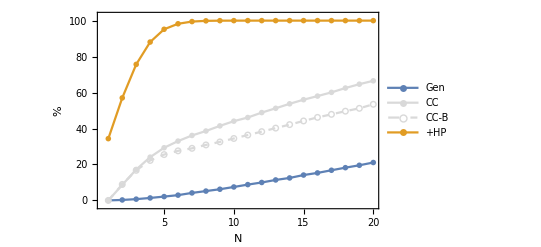

```mathematica
ListPlot[{p1,p2B,p2A,p3},Joined->True,Frame->True,PlotRange->{All,{-2.5,102.5}},FrameLabel->{"N","%"},PlotStyle->{{cd[[1]]}, {LightGray},{Dashed,LightGray},{cd[[2]]}},PlotMarkers->{●,●,○,●},PlotLegends->{"Gen","CC","CC-B","+HP"}]
Export["oscprob.eps",%];
```

## Part 4 : Metaparameters

### Boundaries

```mathematica
mB5 = Import["../boundary/outB5.dat"];
mB2 = Import["../boundary/outB2.dat"];
```

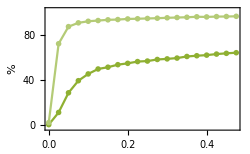

```mathematica
ListPlot[{mB2,mB5},Joined->True,Frame->True,PlotRange->{Automatic,{-2.5,102.5}},FrameLabel->{"Boundary","%"},PlotStyle->{cd[[3]],Lighter[cd[[3]]]},PlotMarkers->{●},ImageSize->250]
Export["boundary.eps",%];
```

### Time constants

```mathematica
mT2 = Import["../timescale/outT2.dat"];
mT5 = Import["../timescale/outT5.dat"];
```

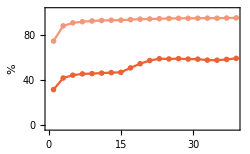

```mathematica
ListPlot[{mT2,mT5},Joined->True,Frame->True,PlotRange->{Automatic,{-2.5,102.5}},FrameLabel->{"Weight and Bias Time-Constants","%"},PlotStyle->{cd[[4]],Lighter[cd[[4]]]},PlotMarkers->{●},ImageSize->250]
Export["timeconstant.eps",%];
```

### Window size for averaging

```mathematica
mW2 = Import["../windowsize/outW2.dat"];
mW5 = Import["../windowsize/outW5.dat"];
```

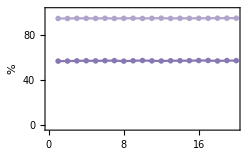

```mathematica
ListPlot[{mW2,mW5},Joined->True,Frame->True,PlotRange->{Automatic,{-2.5,102.5}},FrameLabel->{"Window size for averaging (in timesteps)","%"},PlotStyle->{cd[[5]],Lighter[cd[[5]]]},PlotMarkers->{●},ImageSize->250]
Export["windowsize.eps",%];
```